0.5

1.1

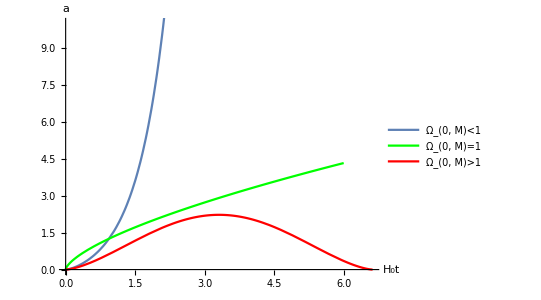

Lambda_matter_universe.pdf

```mathematica
Subscript[Ω, 1]=0.5
Subscript[Ω, 2]=1.1
p2 =Show[ParametricPlot[{{(2*t)/(3*Sqrt[1-Subscript[Ω, 1]]),(Subscript[Ω, 1]/(1-Subscript[Ω, 1]))^(1/3)*Sinh[t]^(3/2)}},{t,0,6},PlotLegends->{"Ω_(0, M)<1"}],Plot[(3/2)^(2/3)t^(2/3),{t,0,6},PlotStyle->Green,PlotLegends->{"Ω_(0, M)=1"}],ParametricPlot[{{(2*t)/(3*Sqrt[Subscript[Ω, 2]-1]),(Subscript[Ω, 2]/(Subscript[Ω, 2]-1))^(1/3)*Sin[t]^(3/2)}},{t,0,6.0},PlotStyle->Red,PlotLegends->{"Ω_(0, M)>1"}],PlotRange->{0,10},AspectRatio->0.75,AxesLabel->{"H_0t",a}]
Export["Lambda_matter_universe.pdf",p2]
```